## Chapter 2 Problem 33: The Double-Square Well

This is part (b) followed by part (c). Part (a) is written out in the solutions manual.

```mathematica
Remove["Global`*"]
```

Set up the problem. The square well has infinite walls at ±a and a square “hump” of height V_0 between ±b

```mathematica
$Assumptions={ϵ>0,m>0,ℏ>0,v>0,a>0,b>0,ϵ<v};
```

```mathematica
aVal=1;
bVal=1/3;
```

```mathematica
eScale=ℏ^2/(2m a^2);
V0Rep=eScale v;
vVal=20;
```

Make a plot of the potential energy. Energy is measured in units eScale.

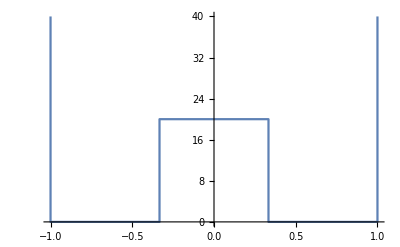

```mathematica
potPlot=ListLinePlot[
{{-aVal,2vVal},{-aVal,0},{-bVal,0},{-bVal,vVal},
{bVal,vVal},
{bVal,0},{aVal,0},{aVal,2vVal}}]
```

Set the wave numbers in and out of the hump

```mathematica
κ=Simplify[Sqrt[2m (V0-ϵ eScale)]/ℏ/.V0->V0Rep];
k=Simplify[Sqrt[2m ϵ eScale]/ℏ];
```

Now find the positive parity solution. First write the form of the wave function.

```mathematica
u1p=A Cosh[κ x];
u2=B Cos[k x]+C Sin[k x];
u2=u2/.Solve[(u2/.x->a)==0,C][[1]];
```

Next find the equations that match the boundary conditions.

```mathematica
eq1=Collect[((u1p/.x->b)-(u2/.x->b)==0)/.{a->aVal,b->bVal},{A,B}];
eq2=Collect[(D[u1p,x]/.x->b)-(D[u2,x]/.x->b)==0/.{a->aVal,b->bVal},{A,B}];
```

These are homogeneous equations for A and B, so set the determinant equal to zero to find ϵ.

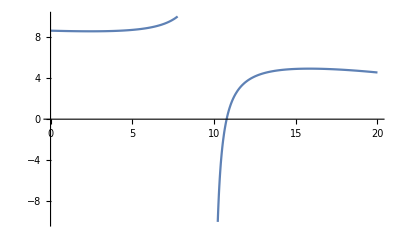

```mathematica
matrixp={Coefficient[eq1[[1]],{A,B}],Coefficient[eq2[[1]],{A,B}]};
det=Det[matrixp/.v->vVal];
Plot[det,{ϵ,0,vVal},PlotRange->{-10,10}]
```

```mathematica
ϵValPos=ϵ/.FindRoot[det,{ϵ,11}]
```

10.7719

Repeat for the negative parity solution

```mathematica
u1n=A Sinh[κ x];
u2=B Cos[k x]+C Sin[k x];
u2=u2/.Solve[(u2/.x->a)==0,C][[1]];
```

```mathematica
eq1=Collect[((u1n/.x->b)-(u2/.x->b)==0)/.{a->aVal,b->bVal},{A,B}];
eq2=Collect[(D[u1n,x]/.x->b)-(D[u2,x]/.x->b)==0/.{a->aVal,b->bVal},{A,B}];
```

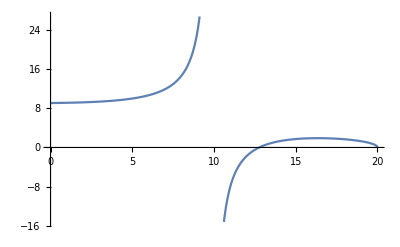

```mathematica
matrixn={Coefficient[eq1[[1]],{A,B}],Coefficient[eq2[[1]],{A,B}]};
det=Det[matrixn/.v->vVal];
Plot[det,{ϵ,0,vVal}]
```

```mathematica
ϵValNeg=ϵ/.FindRoot[det,{ϵ,12}]
```

12.7678

The negative parity solution lies higher than the positive parity solution, as it should. Now plot the normalized wave functions on top of the shape of the potential energy function.

```mathematica
sol=Solve[matrixp[[1]].{A,B}==0,B][[1]];
uPos=Piecewise[{
{u2/.x->-x,x<-bVal},
{u1p,x>-bVal&&x<bVal},
{u2,x>bVal}}]/.sol/.{a->aVal,v->vVal,ϵ->ϵValPos};
normPos=Sqrt[Integrate[Simplify[uPos/A]^2,{x,-aVal,aVal}]];
```

```mathematica
sol=Solve[matrixn[[1]].{A,B}==0,B][[1]];
uNeg=Piecewise[{
{-u2/.x->-x,x<-bVal},
{u1n,x>-bVal&&x<bVal},
{u2,x>bVal}}]/.sol/.{a->aVal,v->vVal,ϵ->ϵValNeg};
normNeg=Sqrt[Integrate[Simplify[uNeg/A]^2,{x,-aVal,aVal}]];
```

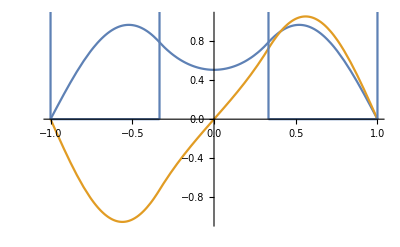

```mathematica
Show[
Plot[{uPos/.A->1/normPos,uNeg/.A->1/normNeg},{x,-aVal,aVal}],
potPlot]
```

These are the curves used to make Fig.4.3 in the textbook.

(c) Now work the problem for V0=10(ℏ^2/2ma^2)

```mathematica
vVal=10;
```

First find the positive parity solution, find the eigenvalue, and plot the eigenfunction

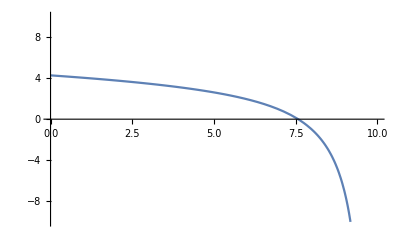

```mathematica
det=Det[matrixp/.v->vVal];
Plot[det,{ϵ,0,vVal},PlotRange->{-10,10}]
```

```mathematica
ϵValPos=ϵ/.FindRoot[det,{ϵ,7}]
```

7.57307

```mathematica
sol=Solve[matrixp[[1]].{A,B}==0,B][[1]];
uPos=Piecewise[{
{u2/.x->-x,x<-bVal},
{u1p,x>-bVal&&x<bVal},
{u2,x>bVal}}]/.sol/.{a->aVal,v->vVal,ϵ->ϵValPos};
normPos=Sqrt[Integrate[Simplify[uPos/A]^2,{x,-aVal,aVal}]];
```

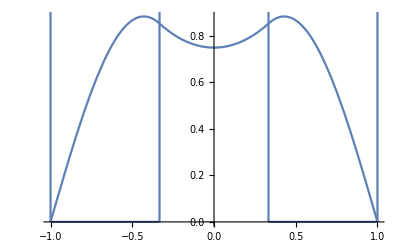

```mathematica
Show[
Plot[uPos/.A->1/normPos,{x,-aVal,aVal}],
potPlot]
```

The curvature inside the barrier is much more shallow this time. What about the negative parity solution?

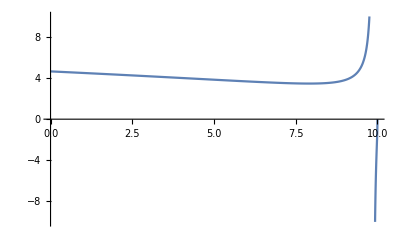

```mathematica
det=Det[matrixn/.v->vVal];
Plot[det,{ϵ,0,vVal},PlotRange->{-10,10}]
```

There is no solution.